# Homework 1

## Problem 2.3

### Graph

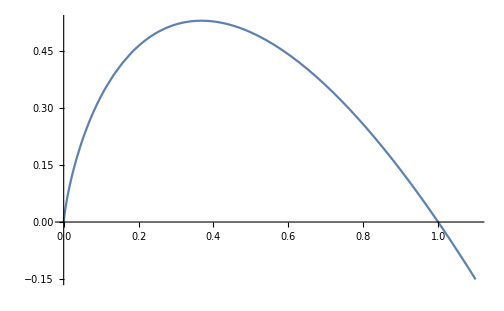

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

## Problem 2.10 (a)

### Definitions

Define a simplification function based on 0≤α≤1

```mathematica
FS10a[aa_]:=FullSimplify[aa,Assumptions->{α∈Reals,0≤α≤1}]
```

Define H(α) in terms of the binary probability function

```mathematica
Hα[pp_]:=-pp Log[2,pp]-(1-pp)Log[2,1-pp]
```

## Problem 2.10 (b)

### Mininize

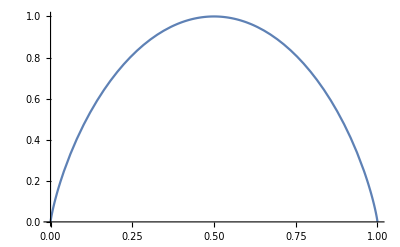

```mathematica
Plot[(Hα[x]),{x,0,1}]
```

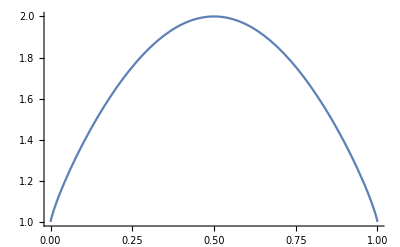

```mathematica
Plot[2^(Hα[x]),{x,0,1}]
```

```mathematica
D[α X1+(1-α)X2,α]//FS10a
```

X1-X2

```mathematica
Solve[D[Hα[α]+α X1+(1-α)X2,α]==0,α]//FS10a
```

{{α→1/(1+2^(-X1+X2))}}

```mathematica
(Hα[α]+(α)(X1+X2))/.Solve[D[Hα[α]+α X1+(1-α)X2,α]==0,α][[1]]//FS10a
(Hα[α]+(1)(X1+X2))/.Solve[D[Hα[α]+α X1+(1-α)X2,α]==0,α][[1]]//FS10a
(Hα[α]+(1+α)(X1+X2))/.Solve[D[Hα[α]+α X1+(1-α)X2,α]==0,α][[1]]//FS10a
```

(-2^X2 Log[1/(1+2^(X1-X2))]+2^X1 ((X1+X2) Log[2]-Log[1/(1+2^(-X1+X2))]))/((2^X1+2^X2) Log[2])

((2^X1+2^X2) (X1+X2) Log[2]-2^X2 Log[1/(1+2^(X1-X2))]-2^X1 Log[1/(1+2^(-X1+X2))])/((2^X1+2^X2) Log[2])

(2^X2 ((X1+X2) Log[2]-Log[1/(1+2^(X1-X2))])+2^X1 ((X1+X2) Log[4]-Log[1/(1+2^(-X1+X2))]))/((2^X1+2^X2) Log[2])

```mathematica
(Hα[α]+α X1+(1-α)X2)/.Solve[D[Hα[α]+α X1+(1-α)X2,α]==0,α][[1]]//FS10a
```

(2^X2 (X2 Log[2]-Log[1/(1+2^(X1-X2))])+2^X1 (X1 Log[2]-Log[1/(1+2^(-X1+X2))]))/((2^X1+2^X2) Log[2])

## Problem 2.24 (b)

### Definitions

Define a simplification function based on 0≤p≤1

```mathematica
FS24b[aa_]:=FullSimplify[aa,Assumptions->{p∈Reals,0≤p≤1}]
```

Define the binary entropy function in terms of base 2 logarithms

```mathematica
H[pp_]:=-pp Log[2,pp]-(1-pp)Log[2,(1-pp)]
H[p]//FS24b
```

((-1+p) Log[1-p]-p Log[p])/Log[2]

Define the binary entropy function in terms of natural logarithms

```mathematica
He[pp_]:=-pp Log[pp]-(1-pp)Log[1-pp]
He[p]//FS24b
```

(-1+p) Log[1-p]-p Log[p]

### Integrate

Using base 2 logarithms

```mathematica
Integrate[H[p],{p,0,1}]//FS24b
Integrate[H[p],{p,0,1}]//FS24b//N
```

1/Log[4]

0.721348

Using natural logarithms

```mathematica
Integrate[He[p],{p,0,1}]//FS24b
Integrate[He[p],{p,0,1}]//FS24b//N
```

1/2

0.5

Checking that changing from nats to bit yields the same result.

```mathematica
(1/2)Log[2,ⅇ]//N
```

0.721348